```mathematica
datos1=Import["C:\\Users\\taldoc\\Downloads\\mec-main\\mec-main\\Dato1e.txt","Data"]
```

{{0.34,0.221},{0.36,0.222},{0.38,0.222},{0.4,0.222},{0.42,0.223},{0.44,0.225},{0.46,0.227},{0.48,0.23},{0.5,0.234},{0.52,0.238},{0.54,0.243},{0.56,0.249},{0.58,0.255},{0.6,0.262},{0.62,0.269},{0.64,0.278},{0.66,0.287},{0.68,0.296},{0.7,0.306},{0.72,0.317},{0.74,0.328},{0.76,0.34},{0.78,0.353},{0.8,0.366},{0.82,0.381},{0.84,0.393},{0.86,0.408},{0.88,0.427},{0.9,0.443},{0.92,0.461},{0.94,0.478},{0.96,0.497},{0.98,0.516},{1.,0.536},{1.02,0.556},{1.04,0.578},{1.06,0.599},{1.08,0.622},{1.1,0.644},{1.12,0.668},{1.14,0.692},{1.16,0.717},{1.18,0.743},{1.2,0.769},{1.22,0.795},{1.24,0.823},{1.26,0.851},{1.28,0.877},{1.3,0.904},{1.32,0.928},{1.34,0.95},{1.36,0.971},{1.38,0.986},{1.4,1.},{1.42,1.011},{1.44,1.018}}

```mathematica
NumDat=Length[datos1]
```

56

```mathematica
DatAj1=Table[datos1[[n]]-datos1[[1]],{n,1,NumDat}]
```

{{0.,0.},{0.02,0.001},{0.04,0.001},{0.06,0.001},{0.08,0.002},{0.1,0.004},{0.12,0.006},{0.14,0.009},{0.16,0.013},{0.18,0.017},{0.2,0.022},{0.22,0.028},{0.24,0.034},{0.26,0.041},{0.28,0.048},{0.3,0.057},{0.32,0.066},{0.34,0.075},{0.36,0.085},{0.38,0.096},{0.4,0.107},{0.42,0.119},{0.44,0.132},{0.46,0.145},{0.48,0.16},{0.5,0.172},{0.52,0.187},{0.54,0.206},{0.56,0.222},{0.58,0.24},{0.6,0.257},{0.62,0.276},{0.64,0.295},{0.66,0.315},{0.68,0.335},{0.7,0.357},{0.72,0.378},{0.74,0.401},{0.76,0.423},{0.78,0.447},{0.8,0.471},{0.82,0.496},{0.84,0.522},{0.86,0.548},{0.88,0.574},{0.9,0.602},{0.92,0.63},{0.94,0.656},{0.96,0.683},{0.98,0.707},{1.,0.729},{1.02,0.75},{1.04,0.765},{1.06,0.779},{1.08,0.79},{1.1,0.797}}

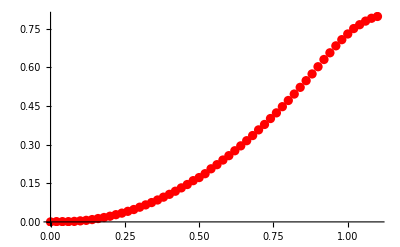

```mathematica
Graf1=ListPlot[DatAj1,PlotStyle->Red]
```

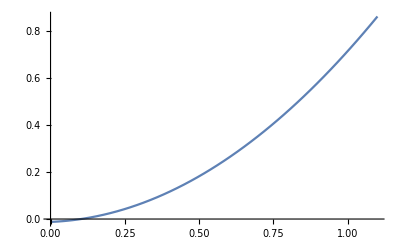

```mathematica
Graf2=Plot[Fun1,{t,0,DatAj1[[NumDat]][[1]]}]
```

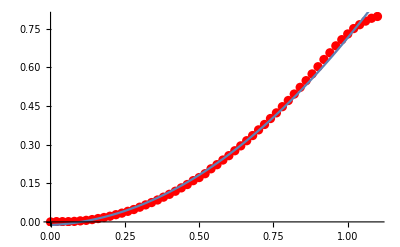

```mathematica
Show[{Graf1,Graf2}]
```

```mathematica
Fun1=Fit[DatAj1,{1,t,t^2},t]
```

-0.0121949+0.0496271 t+0.677141 t^2

```mathematica
PosInici1=Fun1/.t->0
Rap1=D[Fun1,t]
RapInic1=Rap1/.t->0
Acel1=D[Rap1,t]
```

-0.0121949

0.0496271+1.35428 t

0.0496271

1.35428

```mathematica
DatTExp1=Table[DatAj1[[n]][[1]],{n,1,NumDat,1}]
```

{0.,0.02,0.04,0.06,0.08,0.1,0.12,0.14,0.16,0.18,0.2,0.22,0.24,0.26,0.28,0.3,0.32,0.34,0.36,0.38,0.4,0.42,0.44,0.46,0.48,0.5,0.52,0.54,0.56,0.58,0.6,0.62,0.64,0.66,0.68,0.7,0.72,0.74,0.76,0.78,0.8,0.82,0.84,0.86,0.88,0.9,0.92,0.94,0.96,0.98,1.,1.02,1.04,1.06,1.08,1.1}

```mathematica
DatXExp1=Table[DatAj1[[n]][[2]],{n,1,NumDat,1}]
```

{0.,0.001,0.001,0.001,0.002,0.004,0.006,0.009,0.013,0.017,0.022,0.028,0.034,0.041,0.048,0.057,0.066,0.075,0.085,0.096,0.107,0.119,0.132,0.145,0.16,0.172,0.187,0.206,0.222,0.24,0.257,0.276,0.295,0.315,0.335,0.357,0.378,0.401,0.423,0.447,0.471,0.496,0.522,0.548,0.574,0.602,0.63,0.656,0.683,0.707,0.729,0.75,0.765,0.779,0.79,0.797}

```mathematica
DatXAj1=Table[Fun1/.t->DatTExp1[[n]],{n,1,NumDat,1}]
```

{-0.0121949,-0.0109315,-0.00912636,-0.00677954,-0.003891,-0.000460753,0.00351121,0.00802488,0.0130803,0.0186774,0.0248162,0.0314967,0.038719,0.0464829,0.0547886,0.0636359,0.073025,0.0829558,0.0934284,0.104443,0.115999,0.128096,0.140736,0.153917,0.167639,0.181904,0.19671,0.212058,0.227948,0.244379,0.261352,0.278867,0.296923,0.315522,0.334662,0.354343,0.374567,0.395332,0.416638,0.438487,0.460877,0.483809,0.507283,0.531298,0.555855,0.580954,0.606594,0.632776,0.6595,0.686766,0.714573,0.742922,0.771813,0.801246,0.83122,0.861736}

```mathematica
ErrRms1=√(1/NumDat∑_(n=1)^NumDat (DatXExp1[[n]]-DatXAj1[[n]])^2)
```

0.0146689

## Piña Colada